# Blatt 10

Jonas Neundorf & Jan Skottke

Phasenvorschub

Zunächst definieren wir die Linse und den Driftweg.

```mathematica
mF[f_] := {{1, 0}, {-1/f, 1}}(* dünne Linse *)
```

```mathematica
m0[L_] := {{1, L}, {0, 1}} (* Driftmatrix *)
```

Berechne nun die Gesamtmatrix der FODO-Struktur.

```mathematica
fodo = m0[L].mF[-f].m0[L].mF[f] //FullSimplify
```

{{(f^2-f L-L^2)/f^2,(L (2 f+L))/f},{-L/f^2,(f+L)/f}}

Alternativ lässt sich die Entwicklung der Koordinaten auch mit den Twiss-Parametern beschreiben. Nach dem Durchqueren einer FODO-Zelle sollen sie die gleichen Werte wie vorher haben, damit vereinfacht sich die Matrix zu

```mathematica
mM:= {{Cos[ϕ]+α*Sin[ϕ],β*Sin[ϕ]},{-(1+α^2)/β*Sin[ϕ],Cos[ϕ]-α*Sin[ϕ]}}
```

Da beide Matritzen die gleiche Transformation beschreiben, müssen sie gleich sein. Damit ist auch ihre Spur gleich. Daraus lässt sich der Phasenvorschub berechnen.

```mathematica
Solve[Tr[mM] ==Tr[fodo],ϕ]//FullSimplify
```

{{ϕ→ConditionalExpression[-ArcCos[1-L^2/(2 f^2)]+2 π C[1],C[1]∈Integers]},{ϕ→ConditionalExpression[ArcCos[1-L^2/(2 f^2)]+2 π C[1],C[1]∈Integers]}}

```mathematica
rule={ϕ-> ArcCos[1-L^2/(2*f^2)]}
```

{ϕ→ArcCos[1-L^2/(2 f^2)]}

```mathematica
MatrixForm[mM ]== MatrixForm[fodo]
```

(Cos[ϕ]+α Sin[ϕ] | β Sin[ϕ]
-((1+α^2) Sin[ϕ])/β | Cos[ϕ]-α Sin[ϕ])==((f^2-f L-L^2)/f^2 | (L (2 f+L))/f
-L/f^2 | (f+L)/f)

```mathematica
βPhasef = Solve[mM[[1,2]]==fodo[[1,2]],β]
```

{{β→(L (2 f+L) Csc[ϕ])/f}}

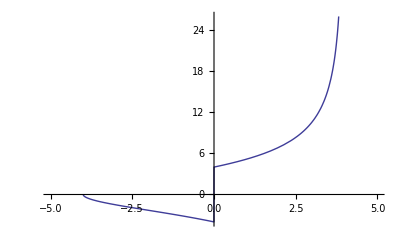

```mathematica
Plot[β//.βPhasef//.rule//.κ-> f/L//.f->2,{L,-5,5}]
```

```mathematica
fo = m0[L].mF[f]
```

{{1-L/f,L},{-1/f,1}}

```mathematica
βPhased= Solve[mM[[1,2]]==fo[[1,2]],β]
```

{{β→L Csc[ϕ]}}

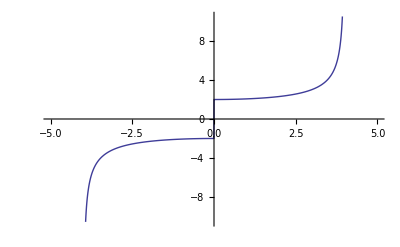

```mathematica
Plot[L*Csc[ϕ]//.rule//.κ-> f/L//.f->2,{L,-5,5}]
```